# Mathematica Bootcamp: Step 6

전경원 박사

Machine Learning Research Engineer
(주)시정
ruddyscent@gmail.com

2021년 10월 18일 월요일

## Access to Lecture Materials

최신 자료는 아래 링크에서 내려받으실 수 있습니다.

https://github.com/ruddyscent/mathematica-bootcamp-2021

## References

체험하며 배우는 WOLFRAM MATHEMATICA
-Graphics-

Wolfram 언어 기초 입문
-Graphics-

Hands-on Start to Mathematica Online, Wolfram U
https://www.wolfram.com/wolfram-u/hands-on-start-to-mathematica-online/

## Probability and Statistics

WolframAlphaQueryResults

-Graphics-
(assuming fair 6-sided dice)

주사위를 던져서 3이 나올 확률은?

```mathematica
Probability[x==3,x\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/6

주사위 두 개를 던져서 합이 12가 나올 확률은?

```mathematica
Probability[x+y==12,x\[Distributed]DiscreteUniformDistribution[{1,6}]&&y\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

1/36

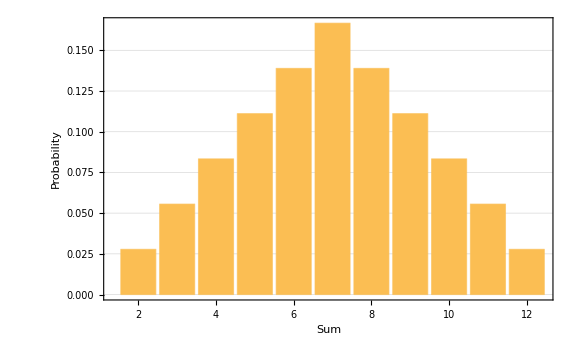

```mathematica
Table[Probability[x+y==result,x\[Distributed]DiscreteUniformDistribution[{1,6}]&&y\[Distributed]DiscreteUniformDistribution[{1,6}]],{result,2,12}];
BarChart[%,ChartLabels->{Range[2,12]},FrameLabel->{"Sum","Probability"},PlotTheme->"Detailed",ImageSize->Large]
```

RandomGeneratorState[…]

{{5,6,2,6,5},{2,4,1,4,6},{4,4,3,3,2},{6,3,3,2,1}}

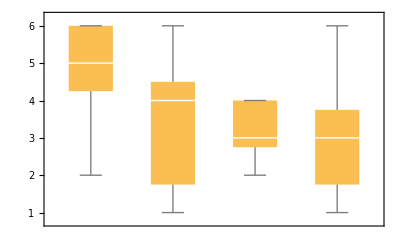

```mathematica
SeedRandom[45]
RandomInteger[{1,6},{4,5}]
BoxWhiskerChart[%,"Outliers"]
```